```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →4, with {} →{-F[9],F[9],V[4],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3,p4}).
However the choice below produces nicer diagrams.

```mathematica
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],V[4],F[9]}];
```

generic model {Lorentz} initialized

classes model {../../FA_models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 3 Particles insertions

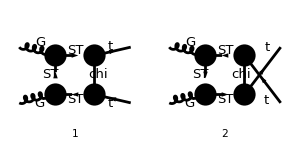

```mathematica
goodDiags=DiagramExtract[allDiags,{2,3}];
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3,p4},LorentzIndexNames->{μ,ν},OutgoingMomenta->{-p2,-p1},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[FCReplaceMomenta[SUNSimplify[DiracSimplify[ampA]],{p4-> -p1-p2-p3}]]]
```

in total: 2 Particles amplitudes

gs^2 yDM^2 (p3^μ-2 q^μ) (p1^ν+p2^ν+p3^ν-2 q^ν) (((T^cc3 T^cc4)_c2c1 ((γ·p2).(γ̄)^6+(γ·p3).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((-p1-p2-p3+q)^2-mST^2).((-p2-p3+q)^2-mChi^2).((q-p3)^2-mST^2))-((T^cc4 T^cc3)_c2c1 ((γ·p1).(γ̄)^6+(γ·p3).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((-p1-p2-p3+q)^2-mST^2).((-p1-p3+q)^2-mChi^2).((q-p3)^2-mST^2)))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, where the top can decay, we will consider only the gluons to be on-shell

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,p3,p4,√p1sq,√p2sq,0,0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]]/.{s+t+u-> p1sq+p2sq};
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(D_0(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | 0
D_0(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | 0
D_1(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0
D_1(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_1(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_1(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_1(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | 0
D_1(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | 0
D_00(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0
D_00(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_11(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0
D_11(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_11(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_11(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_11(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | 0
D_11(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | 0
D_12(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_12(0,0,p2sq,p1sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0
D_12(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_12(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_12(0,t,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_12(0,u,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_001(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0
D_001(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_001(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_001(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_001(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | 0
D_001(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | 0
D_111(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0
D_111(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_111(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_111(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_111(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | 0
D_111(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | 0
D_112(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_112(0,0,p2sq,p1sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0
D_112(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(0,t,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(0,u,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(p1sq,0,0,p2sq,u,s,mChi^2,mST^2,mST^2,mST^2) | 0
D_112(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | 0
D_112(p1sq,t,0,s,0,p2sq,mST^2,mChi^2,mST^2,mST^2) | 0
D_112(p1sq,u,0,s,0,p2sq,mST^2,mChi^2,mST^2,mST^2) | 0
D_112(p2sq,0,0,p1sq,t,s,mChi^2,mST^2,mST^2,mST^2) | 0
D_112(p2sq,p1sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | 0
D_123(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | 0
D_123(0,0,p2sq,p1sq,s,t,mST^2,mST^2,mST^2,mChi^2) | 0)

### Replace D - integrals by short names

```mathematica
argsA={mChi^2,mST^2,mST^2,mST^2};
argsB={mST^2,mChi^2,mST^2,mST^2};
argsC={mST^2,mST^2,mChi^2,mST^2};
argsD={mST^2,mST^2,mST^2,mChi^2};
```

```mathematica
PVsubs ={(PaVe[r_,n1_,n2_,{x1_,x2_,x3_,x4_,x5_,x6_},argsA,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],ToString[n2],"a[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])};
PVsubs=Join[PVsubs,{(PaVe[r_,n1_,n2_,{x1_,x2_,x3_,x4_,x5_,x6_},argsB,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],ToString[n2],"b[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,n1_,n2_,{x1_,x2_,x3_,x4_,x5_,x6_},argsC,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],ToString[n2],"c[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,n1_,n2_,{x1_,x2_,x3_,x4_,x5_,x6_},argsD,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],ToString[n2],"d[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
```

```mathematica
PVsubs=Join[PVsubs,{(PaVe[r_,n1_,{x1_,x2_,x3_,x4_,x5_,x6_},argsA,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],"a[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,n1_,{x1_,x2_,x3_,x4_,x5_,x6_},argsB,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],"b[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,n1_,{x1_,x2_,x3_,x4_,x5_,x6_},argsC,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],"c[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,n1_,{x1_,x2_,x3_,x4_,x5_,x6_},argsD,z___]:>ToExpression[StringJoin[ "D",ToString[r],ToString[n1],"d[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
```

```mathematica
PVsubs=Join[PVsubs,{(PaVe[r_,{x1_,x2_,x3_,x4_,x5_,x6_},argsA,z___]:>ToExpression[StringJoin[ "D",ToString[r],"a[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,{x1_,x2_,x3_,x4_,x5_,x6_},argsB,z___]:>ToExpression[StringJoin[ "D",ToString[r],"b[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,{x1_,x2_,x3_,x4_,x5_,x6_},argsC,z___]:>ToExpression[StringJoin[ "D",ToString[r],"c[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
PVsubs=Join[PVsubs,{(PaVe[r_,{x1_,x2_,x3_,x4_,x5_,x6_},argsD,z___]:>ToExpression[StringJoin[ "D",ToString[r],"d[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]])}];
```

```mathematica
PVsubs=Join[PVsubs,{D0[x1_,x2_,x3_,x4_,x5_,x6_,mST^2,mChi^2,mST^2,mST^2]-> ToExpression[StringJoin["D0b[",ToString[x1],",",ToString[x2],",",ToString[x3],",",ToString[x4],",",ToString[x5],",",ToString[x6],"]"]]}];
```

### Check replacements

```mathematica
Table[{lInts[[i]],lInts[[i]]/.PVsubs},{i,1,Length[lInts]}]
```

(D_0(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | D0b(p1sq,p2sq,0,0,s,t)
D_0(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | D0b(p1sq,p2sq,0,0,s,u)
D_1(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D1d(0,0,p1sq,p2sq,s,t)
D_1(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D1d(0,0,p1sq,p2sq,s,u)
D_1(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | D1c(0,p1sq,p2sq,0,u,s)
D_1(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | D1c(0,p2sq,p1sq,0,t,s)
D_1(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | D1b(p1sq,p2sq,0,0,s,t)
D_1(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | D1b(p1sq,p2sq,0,0,s,u)
D_00(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D00d(0,0,p1sq,p2sq,s,t)
D_00(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D00d(0,0,p1sq,p2sq,s,u)
D_11(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D11d(0,0,p1sq,p2sq,s,t)
D_11(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D11d(0,0,p1sq,p2sq,s,u)
D_11(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | D11c(0,p1sq,p2sq,0,u,s)
D_11(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | D11c(0,p2sq,p1sq,0,t,s)
D_11(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | D11b(p1sq,p2sq,0,0,s,t)
D_11(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | D11b(p1sq,p2sq,0,0,s,u)
D_12(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D12d(0,0,p1sq,p2sq,s,u)
D_12(0,0,p2sq,p1sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D12d(0,0,p2sq,p1sq,s,t)
D_12(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | D12c(0,p1sq,p2sq,0,u,s)
D_12(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | D12c(0,p2sq,p1sq,0,t,s)
D_12(0,t,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | D12c(0,t,p1sq,s,p2sq,0)
D_12(0,u,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | D12c(0,u,p1sq,s,p2sq,0)
D_001(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D001d(0,0,p1sq,p2sq,s,t)
D_001(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D001d(0,0,p1sq,p2sq,s,u)
D_001(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | D001c(0,p1sq,p2sq,0,u,s)
D_001(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | D001c(0,p2sq,p1sq,0,t,s)
D_001(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | D001b(p1sq,p2sq,0,0,s,t)
D_001(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | D001b(p1sq,p2sq,0,0,s,u)
D_111(0,0,p1sq,p2sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D111d(0,0,p1sq,p2sq,s,t)
D_111(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D111d(0,0,p1sq,p2sq,s,u)
D_111(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | D111c(0,p1sq,p2sq,0,u,s)
D_111(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | D111c(0,p2sq,p1sq,0,t,s)
D_111(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | D111b(p1sq,p2sq,0,0,s,t)
D_111(p1sq,p2sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | D111b(p1sq,p2sq,0,0,s,u)
D_112(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D112d(0,0,p1sq,p2sq,s,u)
D_112(0,0,p2sq,p1sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D112d(0,0,p2sq,p1sq,s,t)
D_112(0,p1sq,p2sq,0,u,s,mST^2,mST^2,mChi^2,mST^2) | D112c(0,p1sq,p2sq,0,u,s)
D_112(0,p2sq,p1sq,0,t,s,mST^2,mST^2,mChi^2,mST^2) | D112c(0,p2sq,p1sq,0,t,s)
D_112(0,t,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | D112c(0,t,p1sq,s,p2sq,0)
D_112(0,u,p1sq,s,p2sq,0,mST^2,mST^2,mChi^2,mST^2) | D112c(0,u,p1sq,s,p2sq,0)
D_112(p1sq,0,0,p2sq,u,s,mChi^2,mST^2,mST^2,mST^2) | D112a(p1sq,0,0,p2sq,u,s)
D_112(p1sq,p2sq,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | D112b(p1sq,p2sq,0,0,s,t)
D_112(p1sq,t,0,s,0,p2sq,mST^2,mChi^2,mST^2,mST^2) | D112b(p1sq,t,0,s,0,p2sq)
D_112(p1sq,u,0,s,0,p2sq,mST^2,mChi^2,mST^2,mST^2) | D112b(p1sq,u,0,s,0,p2sq)
D_112(p2sq,0,0,p1sq,t,s,mChi^2,mST^2,mST^2,mST^2) | D112a(p2sq,0,0,p1sq,t,s)
D_112(p2sq,p1sq,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | D112b(p2sq,p1sq,0,0,s,u)
D_123(0,0,p1sq,p2sq,s,u,mST^2,mST^2,mST^2,mChi^2) | D123d(0,0,p1sq,p2sq,s,u)
D_123(0,0,p2sq,p1sq,s,t,mST^2,mST^2,mST^2,mChi^2) | D123d(0,0,p2sq,p1sq,s,t))

```mathematica
ampEsimp3=Simplify[ampEsimp2/.PVsubs];
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]]
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]]
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]]
allTerms=Sort[Join[spinorChains1,spinorChains2]];
pairs1=Cases2[ampEsimp3,Pair]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
pairs2=Flatten[Table[pairs1[[i]] pairs1[[j]],{i,1,Length[pairs1]},{j,i+1,Length[pairs1]}]];
allPairs=Join[pairs1,pairs2];
```

{γ·p1,(γ̄)^6,γ·p3,γ^ν,γ^μ,γ·p2}

{(γ·p1).(γ̄)^6,(γ·p3).(γ̄)^6,γ^ν.(γ̄)^6,γ^μ.(γ̄)^6,(γ·p2).(γ̄)^6}

{}

{g^μν,p1^μ,p2^μ,p3^μ,p1^ν,p2^ν,p3^ν}

{(T^cc3 T^cc4)_c2c1,(T^cc4 T^cc3)_c2c1}

### Coefficients for each term

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
If[Count[c,LorentzIndex[μ,D],Infinity]≠0,Continue[]];
If[Count[c,LorentzIndex[ν,D],Infinity]≠0,Continue[]];
c= Simplify[c/(I Pi^2 gs^2 yDM^2)];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp3]
```

0

```mathematica
su3Terms
```

((T^cc3 T^cc4)_c2c1 | γ^μ.(γ̄)^6 | p1^ν | 2 (2 D001c(0,p1sq,p2sq,0,u,s)+D00d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ̄)^6 | p2^ν | 2 (2 (D001b(p1sq,p2sq,0,0,s,u)+D001c(0,p1sq,p2sq,0,u,s))+D00d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ̄)^6 | p3^ν | -2 (2 D001d(0,0,p1sq,p2sq,s,u)+D00d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | γ^ν.(γ̄)^6 | p1^μ | 4 D001c(0,p1sq,p2sq,0,u,s)
(T^cc3 T^cc4)_c2c1 | γ^ν.(γ̄)^6 | p2^μ | 4 (D001b(p1sq,p2sq,0,0,s,u)+D001c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | γ^ν.(γ̄)^6 | p3^μ | -2 (2 D001d(0,0,p1sq,p2sq,s,u)+D00d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | g^μν | 4 D001c(0,p1sq,p2sq,0,u,s)
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p1^μ p1^ν | 2 (2 D111c(0,p1sq,p2sq,0,u,s)+D11c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p1^μ p2^ν | 2 (2 (D111c(0,p1sq,p2sq,0,u,s)+D112c(0,p1sq,p2sq,0,u,s))+D11c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p1^μ p3^ν | -2 (2 D112a(p1sq,0,0,p2sq,u,s)+D11c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p1^ν p2^μ | 2 (2 D111c(0,p1sq,p2sq,0,u,s)+2 D112c(0,p1sq,p2sq,0,u,s)+D11c(0,p1sq,p2sq,0,u,s)+D12c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p2^μ p2^ν | 2 (2 D111c(0,p1sq,p2sq,0,u,s)+2 D112b(p2sq,p1sq,0,0,s,u)+4 D112c(0,p1sq,p2sq,0,u,s)+D11c(0,p1sq,p2sq,0,u,s)+D12c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p2^μ p3^ν | -2 (2 D112a(p1sq,0,0,p2sq,u,s)+D11c(0,p1sq,p2sq,0,u,s)+2 D123d(0,0,p1sq,p2sq,s,u)+D12c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p1^ν p3^μ | -4 D112a(p1sq,0,0,p2sq,u,s)-2 (D11c(0,p1sq,p2sq,0,u,s)+D12d(0,0,p1sq,p2sq,s,u))-D1c(0,p1sq,p2sq,0,u,s)
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p2^ν p3^μ | -4 D112a(p1sq,0,0,p2sq,u,s)-2 (D11c(0,p1sq,p2sq,0,u,s)+2 D123d(0,0,p1sq,p2sq,s,u)+D12c(0,p1sq,p2sq,0,u,s)+D12d(0,0,p1sq,p2sq,s,u))-D1c(0,p1sq,p2sq,0,u,s)
(T^cc3 T^cc4)_c2c1 | (γ·p1).(γ̄)^6 | p3^μ p3^ν | 4 (D112d(0,0,p1sq,p2sq,s,u)+D12d(0,0,p1sq,p2sq,s,u))+D1c(0,p1sq,p2sq,0,u,s)
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | g^μν | 4 (D001b(p1sq,p2sq,0,0,s,u)+D001c(0,p1sq,p2sq,0,u,s)+D00d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p1^μ p1^ν | 2 (2 D111c(0,p1sq,p2sq,0,u,s)+2 D112c(0,p1sq,p2sq,0,u,s)+3 D11c(0,p1sq,p2sq,0,u,s)+D12c(0,p1sq,p2sq,0,u,s)+D1c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p1^μ p2^ν | 2 (2 D111c(0,p1sq,p2sq,0,u,s)+2 D112b(p2sq,p1sq,0,0,s,u)+4 D112c(0,p1sq,p2sq,0,u,s)+3 (D11c(0,p1sq,p2sq,0,u,s)+D12c(0,p1sq,p2sq,0,u,s))+D1c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p1^μ p3^ν | -2 (2 D112a(p1sq,0,0,p2sq,u,s)+D11c(0,p1sq,p2sq,0,u,s)+2 D123d(0,0,p1sq,p2sq,s,u)+D12c(0,p1sq,p2sq,0,u,s)+2 D12d(0,0,p1sq,p2sq,s,u)+D1c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p1^ν p2^μ | 2 (2 D111c(0,p1sq,p2sq,0,u,s)+2 D112b(p2sq,p1sq,0,0,s,u)+4 D112c(0,p1sq,p2sq,0,u,s)+D11b(p1sq,p2sq,0,0,s,u)+3 D11c(0,p1sq,p2sq,0,u,s)+4 D12c(0,p1sq,p2sq,0,u,s)+D1b(p1sq,p2sq,0,0,s,u)+D1c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p2^μ p2^ν | 2 (2 D111b(p1sq,p2sq,0,0,s,u)+2 D111c(0,p1sq,p2sq,0,u,s)+6 D112b(p2sq,p1sq,0,0,s,u)+6 D112c(0,p1sq,p2sq,0,u,s)+3 D11b(p1sq,p2sq,0,0,s,u)+3 D11c(0,p1sq,p2sq,0,u,s)+6 D12c(0,p1sq,p2sq,0,u,s)+D1b(p1sq,p2sq,0,0,s,u)+D1c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p2^μ p3^ν | -2 (2 D112a(p1sq,0,0,p2sq,u,s)+2 D112b(p1sq,u,0,s,0,p2sq)+D11b(p1sq,p2sq,0,0,s,u)+D11c(0,p1sq,p2sq,0,u,s)+4 D123d(0,0,p1sq,p2sq,s,u)+2 D12c(0,p1sq,p2sq,0,u,s)+2 D12c(0,u,p1sq,s,p2sq,0)+2 D12d(0,0,p1sq,p2sq,s,u)+D1b(p1sq,p2sq,0,0,s,u)+D1c(0,p1sq,p2sq,0,u,s))
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p1^ν p3^μ | -D0b(p1sq,p2sq,0,0,s,u)-4 D112a(p1sq,0,0,p2sq,u,s)-2 D11c(0,p1sq,p2sq,0,u,s)-4 D123d(0,0,p1sq,p2sq,s,u)-2 D12c(0,p1sq,p2sq,0,u,s)-2 D12c(0,u,p1sq,s,p2sq,0)-6 D12d(0,0,p1sq,p2sq,s,u)-D1b(p1sq,p2sq,0,0,s,u)-3 D1c(0,p1sq,p2sq,0,u,s)-2 D1d(0,0,p1sq,p2sq,s,u)
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p2^ν p3^μ | -D0b(p1sq,p2sq,0,0,s,u)-4 D112a(p1sq,0,0,p2sq,u,s)-4 D112b(p1sq,u,0,s,0,p2sq)-2 D11b(p1sq,p2sq,0,0,s,u)-2 D11c(0,p1sq,p2sq,0,u,s)-8 D123d(0,0,p1sq,p2sq,s,u)-3 (2 D12c(0,u,p1sq,s,p2sq,0)+2 D12d(0,0,p1sq,p2sq,s,u)+D1b(p1sq,p2sq,0,0,s,u)+D1c(0,p1sq,p2sq,0,u,s))-4 D12c(0,p1sq,p2sq,0,u,s)-2 D1d(0,0,p1sq,p2sq,s,u)
(T^cc3 T^cc4)_c2c1 | (γ·p2).(γ̄)^6 | p3^μ p3^ν | D0b(p1sq,p2sq,0,0,s,u)+4 D112c(0,u,p1sq,s,p2sq,0)+4 D112d(0,0,p1sq,p2sq,s,u)+4 D11d(0,0,p1sq,p2sq,s,u)+4 D12c(0,u,p1sq,s,p2sq,0)+4 D12d(0,0,p1sq,p2sq,s,u)+D1b(p1sq,p2sq,0,0,s,u)+D1c(0,p1sq,p2sq,0,u,s)+4 D1d(0,0,p1sq,p2sq,s,u)
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | g^μν | -4 D001d(0,0,p1sq,p2sq,s,u)
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p1^μ p1^ν | -2 (2 D112a(p1sq,0,0,p2sq,u,s)+D12d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p1^μ p2^ν | -2 (2 (D112a(p1sq,0,0,p2sq,u,s)+D123d(0,0,p1sq,p2sq,s,u))+D12d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p1^μ p3^ν | 2 (2 D112d(0,0,p1sq,p2sq,s,u)+D12d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p1^ν p2^μ | -2 (2 D112a(p1sq,0,0,p2sq,u,s)+2 D123d(0,0,p1sq,p2sq,s,u)+D12c(0,u,p1sq,s,p2sq,0)+D12d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p2^μ p2^ν | -2 (2 D112a(p1sq,0,0,p2sq,u,s)+2 D112b(p1sq,u,0,s,0,p2sq)+4 D123d(0,0,p1sq,p2sq,s,u)+D12c(0,u,p1sq,s,p2sq,0)+D12d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p2^μ p3^ν | 2 (2 D112c(0,u,p1sq,s,p2sq,0)+2 D112d(0,0,p1sq,p2sq,s,u)+D12c(0,u,p1sq,s,p2sq,0)+D12d(0,0,p1sq,p2sq,s,u))
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p1^ν p3^μ | 4 D112d(0,0,p1sq,p2sq,s,u)+2 (D11d(0,0,p1sq,p2sq,s,u)+D12d(0,0,p1sq,p2sq,s,u))+D1d(0,0,p1sq,p2sq,s,u)
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p2^ν p3^μ | 4 D112c(0,u,p1sq,s,p2sq,0)+4 D112d(0,0,p1sq,p2sq,s,u)+2 (D11d(0,0,p1sq,p2sq,s,u)+D12c(0,u,p1sq,s,p2sq,0)+D12d(0,0,p1sq,p2sq,s,u))+D1d(0,0,p1sq,p2sq,s,u)
(T^cc3 T^cc4)_c2c1 | (γ·p3).(γ̄)^6 | p3^μ p3^ν | -4 (D111d(0,0,p1sq,p2sq,s,u)+D11d(0,0,p1sq,p2sq,s,u))-D1d(0,0,p1sq,p2sq,s,u)
(T^cc4 T^cc3)_c2c1 | γ^μ.(γ̄)^6 | p1^ν | -2 (2 (D001b(p1sq,p2sq,0,0,s,t)+D001c(0,p2sq,p1sq,0,t,s))+D00d(0,0,p1sq,p2sq,s,t))
(T^cc4 T^cc3)_c2c1 | γ^μ.(γ̄)^6 | p2^ν | -2 (2 D001c(0,p2sq,p1sq,0,t,s)+D00d(0,0,p1sq,p2sq,s,t))
(T^cc4 T^cc3)_c2c1 | γ^μ.(γ̄)^6 | p3^ν | 2 (2 D001d(0,0,p1sq,p2sq,s,t)+D00d(0,0,p1sq,p2sq,s,t))
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ̄)^6 | p1^μ | -4 (D001b(p1sq,p2sq,0,0,s,t)+D001c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ̄)^6 | p2^μ | -4 D001c(0,p2sq,p1sq,0,t,s)
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ̄)^6 | p3^μ | 2 (2 D001d(0,0,p1sq,p2sq,s,t)+D00d(0,0,p1sq,p2sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | g^μν | -4 (D001b(p1sq,p2sq,0,0,s,t)+D001c(0,p2sq,p1sq,0,t,s)+D00d(0,0,p1sq,p2sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p1^μ p1^ν | -2 (2 D111b(p1sq,p2sq,0,0,s,t)+2 D111c(0,p2sq,p1sq,0,t,s)+6 D112b(p1sq,p2sq,0,0,s,t)+6 D112c(0,p2sq,p1sq,0,t,s)+3 D11b(p1sq,p2sq,0,0,s,t)+3 D11c(0,p2sq,p1sq,0,t,s)+6 D12c(0,p2sq,p1sq,0,t,s)+D1b(p1sq,p2sq,0,0,s,t)+D1c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p1^μ p2^ν | -2 (2 D111c(0,p2sq,p1sq,0,t,s)+2 D112b(p1sq,p2sq,0,0,s,t)+4 D112c(0,p2sq,p1sq,0,t,s)+D11b(p1sq,p2sq,0,0,s,t)+3 D11c(0,p2sq,p1sq,0,t,s)+4 D12c(0,p2sq,p1sq,0,t,s)+D1b(p1sq,p2sq,0,0,s,t)+D1c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p1^μ p3^ν | 2 (2 D112a(p2sq,0,0,p1sq,t,s)+2 D112b(p1sq,t,0,s,0,p2sq)+D11b(p1sq,p2sq,0,0,s,t)+D11c(0,p2sq,p1sq,0,t,s)+4 D123d(0,0,p2sq,p1sq,s,t)+2 D12c(0,p2sq,p1sq,0,t,s)+2 D12c(0,t,p1sq,s,p2sq,0)+2 D12d(0,0,p2sq,p1sq,s,t)+D1b(p1sq,p2sq,0,0,s,t)+D1c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p1^ν p2^μ | -2 (2 D111c(0,p2sq,p1sq,0,t,s)+2 D112b(p1sq,p2sq,0,0,s,t)+4 D112c(0,p2sq,p1sq,0,t,s)+3 (D11c(0,p2sq,p1sq,0,t,s)+D12c(0,p2sq,p1sq,0,t,s))+D1c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p2^μ p2^ν | -2 (2 D111c(0,p2sq,p1sq,0,t,s)+2 D112c(0,p2sq,p1sq,0,t,s)+3 D11c(0,p2sq,p1sq,0,t,s)+D12c(0,p2sq,p1sq,0,t,s)+D1c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p2^μ p3^ν | 2 (2 D112a(p2sq,0,0,p1sq,t,s)+D11c(0,p2sq,p1sq,0,t,s)+2 D123d(0,0,p2sq,p1sq,s,t)+D12c(0,p2sq,p1sq,0,t,s)+2 D12d(0,0,p2sq,p1sq,s,t)+D1c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p1^ν p3^μ | D0b(p1sq,p2sq,0,0,s,t)+4 D112a(p2sq,0,0,p1sq,t,s)+4 D112b(p1sq,t,0,s,0,p2sq)+2 D11b(p1sq,p2sq,0,0,s,t)+2 D11c(0,p2sq,p1sq,0,t,s)+8 D123d(0,0,p2sq,p1sq,s,t)+3 (2 D12c(0,t,p1sq,s,p2sq,0)+2 D12d(0,0,p2sq,p1sq,s,t)+D1b(p1sq,p2sq,0,0,s,t)+D1c(0,p2sq,p1sq,0,t,s))+4 D12c(0,p2sq,p1sq,0,t,s)+2 D1d(0,0,p1sq,p2sq,s,t)
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p2^ν p3^μ | D0b(p1sq,p2sq,0,0,s,t)+4 D112a(p2sq,0,0,p1sq,t,s)+2 D11c(0,p2sq,p1sq,0,t,s)+4 D123d(0,0,p2sq,p1sq,s,t)+2 D12c(0,p2sq,p1sq,0,t,s)+2 D12c(0,t,p1sq,s,p2sq,0)+6 D12d(0,0,p2sq,p1sq,s,t)+D1b(p1sq,p2sq,0,0,s,t)+3 D1c(0,p2sq,p1sq,0,t,s)+2 D1d(0,0,p1sq,p2sq,s,t)
(T^cc4 T^cc3)_c2c1 | (γ·p1).(γ̄)^6 | p3^μ p3^ν | -D0b(p1sq,p2sq,0,0,s,t)-4 D112c(0,t,p1sq,s,p2sq,0)-4 D112d(0,0,p2sq,p1sq,s,t)-4 D11d(0,0,p1sq,p2sq,s,t)-4 D12c(0,t,p1sq,s,p2sq,0)-4 D12d(0,0,p2sq,p1sq,s,t)-D1b(p1sq,p2sq,0,0,s,t)-D1c(0,p2sq,p1sq,0,t,s)-4 D1d(0,0,p1sq,p2sq,s,t)
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | g^μν | -4 D001c(0,p2sq,p1sq,0,t,s)
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p1^μ p1^ν | -2 (2 D111c(0,p2sq,p1sq,0,t,s)+2 D112b(p1sq,p2sq,0,0,s,t)+4 D112c(0,p2sq,p1sq,0,t,s)+D11c(0,p2sq,p1sq,0,t,s)+D12c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p1^μ p2^ν | -2 (2 D111c(0,p2sq,p1sq,0,t,s)+2 D112c(0,p2sq,p1sq,0,t,s)+D11c(0,p2sq,p1sq,0,t,s)+D12c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p1^μ p3^ν | 2 (2 D112a(p2sq,0,0,p1sq,t,s)+D11c(0,p2sq,p1sq,0,t,s)+2 D123d(0,0,p2sq,p1sq,s,t)+D12c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p1^ν p2^μ | -2 (2 (D111c(0,p2sq,p1sq,0,t,s)+D112c(0,p2sq,p1sq,0,t,s))+D11c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p2^μ p2^ν | -2 (2 D111c(0,p2sq,p1sq,0,t,s)+D11c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p2^μ p3^ν | 2 (2 D112a(p2sq,0,0,p1sq,t,s)+D11c(0,p2sq,p1sq,0,t,s))
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p1^ν p3^μ | 4 D112a(p2sq,0,0,p1sq,t,s)+2 (D11c(0,p2sq,p1sq,0,t,s)+2 D123d(0,0,p2sq,p1sq,s,t)+D12c(0,p2sq,p1sq,0,t,s)+D12d(0,0,p2sq,p1sq,s,t))+D1c(0,p2sq,p1sq,0,t,s)
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p2^ν p3^μ | 4 D112a(p2sq,0,0,p1sq,t,s)+2 (D11c(0,p2sq,p1sq,0,t,s)+D12d(0,0,p2sq,p1sq,s,t))+D1c(0,p2sq,p1sq,0,t,s)
(T^cc4 T^cc3)_c2c1 | (γ·p2).(γ̄)^6 | p3^μ p3^ν | -4 (D112d(0,0,p2sq,p1sq,s,t)+D12d(0,0,p2sq,p1sq,s,t))-D1c(0,p2sq,p1sq,0,t,s)
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | g^μν | 4 D001d(0,0,p1sq,p2sq,s,t)
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p1^μ p1^ν | 2 (2 D112a(p2sq,0,0,p1sq,t,s)+2 D112b(p1sq,t,0,s,0,p2sq)+4 D123d(0,0,p2sq,p1sq,s,t)+D12c(0,t,p1sq,s,p2sq,0)+D12d(0,0,p2sq,p1sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p1^μ p2^ν | 2 (2 D112a(p2sq,0,0,p1sq,t,s)+2 D123d(0,0,p2sq,p1sq,s,t)+D12c(0,t,p1sq,s,p2sq,0)+D12d(0,0,p2sq,p1sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p1^μ p3^ν | -2 (2 D112c(0,t,p1sq,s,p2sq,0)+2 D112d(0,0,p2sq,p1sq,s,t)+D12c(0,t,p1sq,s,p2sq,0)+D12d(0,0,p2sq,p1sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p1^ν p2^μ | 2 (2 (D112a(p2sq,0,0,p1sq,t,s)+D123d(0,0,p2sq,p1sq,s,t))+D12d(0,0,p2sq,p1sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p2^μ p2^ν | 2 (2 D112a(p2sq,0,0,p1sq,t,s)+D12d(0,0,p2sq,p1sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p2^μ p3^ν | -2 (2 D112d(0,0,p2sq,p1sq,s,t)+D12d(0,0,p2sq,p1sq,s,t))
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p1^ν p3^μ | -4 D112c(0,t,p1sq,s,p2sq,0)-4 D112d(0,0,p2sq,p1sq,s,t)-2 (D11d(0,0,p1sq,p2sq,s,t)+D12c(0,t,p1sq,s,p2sq,0)+D12d(0,0,p2sq,p1sq,s,t))-D1d(0,0,p1sq,p2sq,s,t)
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p2^ν p3^μ | -4 D112d(0,0,p2sq,p1sq,s,t)-2 (D11d(0,0,p1sq,p2sq,s,t)+D12d(0,0,p2sq,p1sq,s,t))-D1d(0,0,p1sq,p2sq,s,t)
(T^cc4 T^cc3)_c2c1 | (γ·p3).(γ̄)^6 | p3^μ p3^ν | 4 (D111d(0,0,p1sq,p2sq,s,t)+D11d(0,0,p1sq,p2sq,s,t))+D1d(0,0,p1sq,p2sq,s,t))

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3), p4(ν)=P(*,4) ] (all momenta are incoming)
 c1 = Anti-Top color = “1”, c2 = Top color = “2”, c3 = Gluon color = “3”, c4 = Gluon color = “4”
spins = [2, 2, 3], 
structure = ‘ P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)’)

s = (p1+p2)^2 =  P(-1,1)**2 + P(-1,2)**2 + 2*P(-1,1)*P(-1,2)
t = (p1+p3)^2  = P(-1,1)**2 + P(-1,3)**2 + 2*P(-1,1)*P(-1,3)
u = (p1+p4)^2  = (p2+p3)^2 = P(-1,2)**2 + P(-1,3)**2 + 2*P(-1,2)*P(-1,3) 
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contract to the left and the first (incoming) to the right)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
momenta=Tally[su3Terms[[All,3]]][[All,1]]
```

{(T^cc3 T^cc4)_c2c1,(T^cc4 T^cc3)_c2c1}

{γ^μ.(γ̄)^6,γ^ν.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p3).(γ̄)^6}

{p1^ν,p2^ν,p3^ν,p1^μ,p2^μ,p3^μ,g^μν,p1^μ p1^ν,p1^μ p2^ν,p1^μ p3^ν,p1^ν p2^μ,p2^μ p2^ν,p2^μ p3^ν,p1^ν p3^μ,p2^ν p3^μ,p3^μ p3^ν}

```mathematica
su3Replacements={SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]]-> "T(3,2,-1)*T(4,-1,1)",
                                   SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]->  "T(4,2,-1)*T(3,-1,1)"};
tensorReplacements={DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6]-> "Gamma(3,2,-1)*ProjP(-1,1)",
DiracGamma[LorentzIndex[ν,D],D].DiracGamma[6]-> "Gamma(4,2,-1)*ProjP(-1,1)",
DiracGamma[Momentum[p1,D],D].DiracGamma[6]-> "P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1)",
DiracGamma[Momentum[p2,D],D].DiracGamma[6]-> "P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1)",
DiracGamma[Momentum[p3,D],D].DiracGamma[6]-> "P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1)"};
momentaReplacements={Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-> "Metric(3,4)*",
				      Pair[LorentzIndex[ν,D],Momentum[p1,D]]-> "P(4,1)*",
				       Pair[LorentzIndex[μ,D],Momentum[p1,D]]-> "P(3,1)*",
				      Pair[LorentzIndex[ν,D],Momentum[p2,D]]-> "P(4,2)*",
				       Pair[LorentzIndex[μ,D],Momentum[p2,D]]-> "P(3,2)*",
				       Pair[LorentzIndex[ν,D],Momentum[p3,D]]-> "P(4,3)*",
				       Pair[LorentzIndex[μ,D],Momentum[p3,D]]-> "P(3,3)*"
				    };
```

```mathematica
tensorReplacements
momentaReplacements
```

{γ^μ.(γ̄)^6→Gamma(3,2,-1)*ProjP(-1,1),γ^ν.(γ̄)^6→Gamma(4,2,-1)*ProjP(-1,1),(γ·p1).(γ̄)^6→P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1),(γ·p2).(γ̄)^6→P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1),(γ·p3).(γ̄)^6→P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1)}

{g^μν→Metric(3,4)*,p1^ν→P(4,1)*,p1^μ→P(3,1)*,p2^ν→P(4,2)*,p2^μ→P(3,2)*,p3^ν→P(4,3)*,p3^μ→P(3,3)*}

### Print each Lorentz structure as a distinct Lorentz vertex :

```mathematica
vertexCounter=0;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Print[StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n      +   "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*(\\\n  ",fullStr,"\\\n  )"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,-1)*T(4,-1,1)

FFVVNP1

( Gamma(3,2,-1)*ProjP(-1,1) )*(\
  P(4,1)*(2*(2*D001c(0,p1sq,p2sq,0,u,s) + D00d(0,0,p1sq,p2sq,s,u)))\
      +   P(4,2)*(2*(2*(D001b(p1sq,p2sq,0,0,s,u) + D001c(0,p1sq,p2sq,0,u,s)) + D00d(0,0,p1sq,p2sq,s,u)))\
      +   P(4,3)*(-2*(2*D001d(0,0,p1sq,p2sq,s,u) + D00d(0,0,p1sq,p2sq,s,u)))\
  )

FFVVNP2

( Gamma(4,2,-1)*ProjP(-1,1) )*(\
  P(3,1)*(4*D001c(0,p1sq,p2sq,0,u,s))\
      +   P(3,2)*(4*(D001b(p1sq,p2sq,0,0,s,u) + D001c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,3)*(-2*(2*D001d(0,0,p1sq,p2sq,s,u) + D00d(0,0,p1sq,p2sq,s,u)))\
  )

FFVVNP3

( P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(4*D001c(0,p1sq,p2sq,0,u,s))\
      +   P(3,1)*P(4,1)*(2*(2*D111c(0,p1sq,p2sq,0,u,s) + D11c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,1)*P(4,2)*(2*(2*(D111c(0,p1sq,p2sq,0,u,s) + D112c(0,p1sq,p2sq,0,u,s)) + D11c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,1)*P(4,3)*(-2*(2*D112a(p1sq,0,0,p2sq,u,s) + D11c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,2)*P(4,1)*(2*(2*D111c(0,p1sq,p2sq,0,u,s) + 2*D112c(0,p1sq,p2sq,0,u,s) + D11c(0,p1sq,p2sq,0,u,s) + D12c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,2)*P(4,2)*(2*(2*D111c(0,p1sq,p2sq,0,u,s) + 2*D112b(p2sq,p1sq,0,0,s,u) + 4*D112c(0,p1sq,p2sq,0,u,s) + D11c(0,p1sq,p2sq,0,u,s) + D12c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,2)*P(4,3)*(-2*(2*D112a(p1sq,0,0,p2sq,u,s) + D11c(0,p1sq,p2sq,0,u,s) + 2*D123d(0,0,p1sq,p2sq,s,u) + D12c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,3)*P(4,1)*(-4*D112a(p1sq,0,0,p2sq,u,s) - 2*(D11c(0,p1sq,p2sq,0,u,s) + D12d(0,0,p1sq,p2sq,s,u)) - D1c(0,p1sq,p2sq,0,u,s))\
      +   P(3,3)*P(4,2)*(-4*D112a(p1sq,0,0,p2sq,u,s) - 2*(D11c(0,p1sq,p2sq,0,u,s) + 2*D123d(0,0,p1sq,p2sq,s,u) + D12c(0,p1sq,p2sq,0,u,s) + D12d(0,0,p1sq,p2sq,s,u)) - D1c(0,p1sq,p2sq,0,u,s))\
      +   P(3,3)*P(4,3)*(4*(D112d(0,0,p1sq,p2sq,s,u) + D12d(0,0,p1sq,p2sq,s,u)) + D1c(0,p1sq,p2sq,0,u,s))\
  )

FFVVNP4

( P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(4*(D001b(p1sq,p2sq,0,0,s,u) + D001c(0,p1sq,p2sq,0,u,s) + D00d(0,0,p1sq,p2sq,s,u)))\
      +   P(3,1)*P(4,1)*(2*(2*D111c(0,p1sq,p2sq,0,u,s) + 2*D112c(0,p1sq,p2sq,0,u,s) + 3*D11c(0,p1sq,p2sq,0,u,s) + D12c(0,p1sq,p2sq,0,u,s) + D1c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,1)*P(4,2)*(2*(2*D111c(0,p1sq,p2sq,0,u,s) + 2*D112b(p2sq,p1sq,0,0,s,u) + 4*D112c(0,p1sq,p2sq,0,u,s) + 3*(D11c(0,p1sq,p2sq,0,u,s) + D12c(0,p1sq,p2sq,0,u,s)) + D1c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,1)*P(4,3)*(-2*(2*D112a(p1sq,0,0,p2sq,u,s) + D11c(0,p1sq,p2sq,0,u,s) + 2*D123d(0,0,p1sq,p2sq,s,u) + D12c(0,p1sq,p2sq,0,u,s) + 2*D12d(0,0,p1sq,p2sq,s,u) + D1c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,2)*P(4,1)*(2*(2*D111c(0,p1sq,p2sq,0,u,s) + 2*D112b(p2sq,p1sq,0,0,s,u) + 4*D112c(0,p1sq,p2sq,0,u,s) + D11b(p1sq,p2sq,0,0,s,u) + 3*D11c(0,p1sq,p2sq,0,u,s) + 4*D12c(0,p1sq,p2sq,0,u,s) + D1b(p1sq,p2sq,0,0,s,u) + D1c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,2)*P(4,2)*(2*(2*D111b(p1sq,p2sq,0,0,s,u) + 2*D111c(0,p1sq,p2sq,0,u,s) + 6*D112b(p2sq,p1sq,0,0,s,u) + 6*D112c(0,p1sq,p2sq,0,u,s) + 3*D11b(p1sq,p2sq,0,0,s,u) + 3*D11c(0,p1sq,p2sq,0,u,s) + 6*D12c(0,p1sq,p2sq,0,u,s) + D1b(p1sq,p2sq,0,0,s,u) + D1c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,2)*P(4,3)*(-2*(2*D112a(p1sq,0,0,p2sq,u,s) + 2*D112b(p1sq,u,0,s,0,p2sq) + D11b(p1sq,p2sq,0,0,s,u) + D11c(0,p1sq,p2sq,0,u,s) + 4*D123d(0,0,p1sq,p2sq,s,u) + 2*D12c(0,p1sq,p2sq,0,u,s) + 2*D12c(0,u,p1sq,s,p2sq,0) + 2*D12d(0,0,p1sq,p2sq,s,u) + D1b(p1sq,p2sq,0,0,s,u) + D1c(0,p1sq,p2sq,0,u,s)))\
      +   P(3,3)*P(4,1)*(-D0b(p1sq,p2sq,0,0,s,u) - 4*D112a(p1sq,0,0,p2sq,u,s) - 2*D11c(0,p1sq,p2sq,0,u,s) - 4*D123d(0,0,p1sq,p2sq,s,u) - 2*D12c(0,p1sq,p2sq,0,u,s) - 2*D12c(0,u,p1sq,s,p2sq,0) - 6*D12d(0,0,p1sq,p2sq,s,u) - D1b(p1sq,p2sq,0,0,s,u) - 3*D1c(0,p1sq,p2sq,0,u,s) - 2*D1d(0,0,p1sq,p2sq,s,u))\
      +   P(3,3)*P(4,2)*(-D0b(p1sq,p2sq,0,0,s,u) - 4*D112a(p1sq,0,0,p2sq,u,s) - 4*D112b(p1sq,u,0,s,0,p2sq) - 2*D11b(p1sq,p2sq,0,0,s,u) - 2*D11c(0,p1sq,p2sq,0,u,s) - 8*D123d(0,0,p1sq,p2sq,s,u) - 4*D12c(0,p1sq,p2sq,0,u,s) - 3*(2*D12c(0,u,p1sq,s,p2sq,0) + 2*D12d(0,0,p1sq,p2sq,s,u) + D1b(p1sq,p2sq,0,0,s,u) + D1c(0,p1sq,p2sq,0,u,s)) - 2*D1d(0,0,p1sq,p2sq,s,u))\
      +   P(3,3)*P(4,3)*(D0b(p1sq,p2sq,0,0,s,u) + 4*D112c(0,u,p1sq,s,p2sq,0) + 4*D112d(0,0,p1sq,p2sq,s,u) + 4*D11d(0,0,p1sq,p2sq,s,u) + 4*D12c(0,u,p1sq,s,p2sq,0) + 4*D12d(0,0,p1sq,p2sq,s,u) + D1b(p1sq,p2sq,0,0,s,u) + D1c(0,p1sq,p2sq,0,u,s) + 4*D1d(0,0,p1sq,p2sq,s,u))\
  )

FFVVNP5

( P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(-4*D001d(0,0,p1sq,p2sq,s,u))\
      +   P(3,1)*P(4,1)*(-2*(2*D112a(p1sq,0,0,p2sq,u,s) + D12d(0,0,p1sq,p2sq,s,u)))\
      +   P(3,1)*P(4,2)*(-2*(2*(D112a(p1sq,0,0,p2sq,u,s) + D123d(0,0,p1sq,p2sq,s,u)) + D12d(0,0,p1sq,p2sq,s,u)))\
      +   P(3,1)*P(4,3)*(2*(2*D112d(0,0,p1sq,p2sq,s,u) + D12d(0,0,p1sq,p2sq,s,u)))\
      +   P(3,2)*P(4,1)*(-2*(2*D112a(p1sq,0,0,p2sq,u,s) + 2*D123d(0,0,p1sq,p2sq,s,u) + D12c(0,u,p1sq,s,p2sq,0) + D12d(0,0,p1sq,p2sq,s,u)))\
      +   P(3,2)*P(4,2)*(-2*(2*D112a(p1sq,0,0,p2sq,u,s) + 2*D112b(p1sq,u,0,s,0,p2sq) + 4*D123d(0,0,p1sq,p2sq,s,u) + D12c(0,u,p1sq,s,p2sq,0) + D12d(0,0,p1sq,p2sq,s,u)))\
      +   P(3,2)*P(4,3)*(2*(2*D112c(0,u,p1sq,s,p2sq,0) + 2*D112d(0,0,p1sq,p2sq,s,u) + D12c(0,u,p1sq,s,p2sq,0) + D12d(0,0,p1sq,p2sq,s,u)))\
      +   P(3,3)*P(4,1)*(4*D112d(0,0,p1sq,p2sq,s,u) + 2*(D11d(0,0,p1sq,p2sq,s,u) + D12d(0,0,p1sq,p2sq,s,u)) + D1d(0,0,p1sq,p2sq,s,u))\
      +   P(3,3)*P(4,2)*(4*D112c(0,u,p1sq,s,p2sq,0) + 4*D112d(0,0,p1sq,p2sq,s,u) + 2*(D11d(0,0,p1sq,p2sq,s,u) + D12c(0,u,p1sq,s,p2sq,0) + D12d(0,0,p1sq,p2sq,s,u)) + D1d(0,0,p1sq,p2sq,s,u))\
      +   P(3,3)*P(4,3)*(-4*(D111d(0,0,p1sq,p2sq,s,u) + D11d(0,0,p1sq,p2sq,s,u)) - D1d(0,0,p1sq,p2sq,s,u))\
  )

------------------

T(4,2,-1)*T(3,-1,1)

FFVVNP6

( Gamma(3,2,-1)*ProjP(-1,1) )*(\
  P(4,1)*(-2*(2*(D001b(p1sq,p2sq,0,0,s,t) + D001c(0,p2sq,p1sq,0,t,s)) + D00d(0,0,p1sq,p2sq,s,t)))\
      +   P(4,2)*(-2*(2*D001c(0,p2sq,p1sq,0,t,s) + D00d(0,0,p1sq,p2sq,s,t)))\
      +   P(4,3)*(2*(2*D001d(0,0,p1sq,p2sq,s,t) + D00d(0,0,p1sq,p2sq,s,t)))\
  )

FFVVNP7

( Gamma(4,2,-1)*ProjP(-1,1) )*(\
  P(3,1)*(-4*(D001b(p1sq,p2sq,0,0,s,t) + D001c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,2)*(-4*D001c(0,p2sq,p1sq,0,t,s))\
      +   P(3,3)*(2*(2*D001d(0,0,p1sq,p2sq,s,t) + D00d(0,0,p1sq,p2sq,s,t)))\
  )

FFVVNP8

( P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(-4*(D001b(p1sq,p2sq,0,0,s,t) + D001c(0,p2sq,p1sq,0,t,s) + D00d(0,0,p1sq,p2sq,s,t)))\
      +   P(3,1)*P(4,1)*(-2*(2*D111b(p1sq,p2sq,0,0,s,t) + 2*D111c(0,p2sq,p1sq,0,t,s) + 6*D112b(p1sq,p2sq,0,0,s,t) + 6*D112c(0,p2sq,p1sq,0,t,s) + 3*D11b(p1sq,p2sq,0,0,s,t) + 3*D11c(0,p2sq,p1sq,0,t,s) + 6*D12c(0,p2sq,p1sq,0,t,s) + D1b(p1sq,p2sq,0,0,s,t) + D1c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,1)*P(4,2)*(-2*(2*D111c(0,p2sq,p1sq,0,t,s) + 2*D112b(p1sq,p2sq,0,0,s,t) + 4*D112c(0,p2sq,p1sq,0,t,s) + D11b(p1sq,p2sq,0,0,s,t) + 3*D11c(0,p2sq,p1sq,0,t,s) + 4*D12c(0,p2sq,p1sq,0,t,s) + D1b(p1sq,p2sq,0,0,s,t) + D1c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,1)*P(4,3)*(2*(2*D112a(p2sq,0,0,p1sq,t,s) + 2*D112b(p1sq,t,0,s,0,p2sq) + D11b(p1sq,p2sq,0,0,s,t) + D11c(0,p2sq,p1sq,0,t,s) + 4*D123d(0,0,p2sq,p1sq,s,t) + 2*D12c(0,p2sq,p1sq,0,t,s) + 2*D12c(0,t,p1sq,s,p2sq,0) + 2*D12d(0,0,p2sq,p1sq,s,t) + D1b(p1sq,p2sq,0,0,s,t) + D1c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,2)*P(4,1)*(-2*(2*D111c(0,p2sq,p1sq,0,t,s) + 2*D112b(p1sq,p2sq,0,0,s,t) + 4*D112c(0,p2sq,p1sq,0,t,s) + 3*(D11c(0,p2sq,p1sq,0,t,s) + D12c(0,p2sq,p1sq,0,t,s)) + D1c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,2)*P(4,2)*(-2*(2*D111c(0,p2sq,p1sq,0,t,s) + 2*D112c(0,p2sq,p1sq,0,t,s) + 3*D11c(0,p2sq,p1sq,0,t,s) + D12c(0,p2sq,p1sq,0,t,s) + D1c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,2)*P(4,3)*(2*(2*D112a(p2sq,0,0,p1sq,t,s) + D11c(0,p2sq,p1sq,0,t,s) + 2*D123d(0,0,p2sq,p1sq,s,t) + D12c(0,p2sq,p1sq,0,t,s) + 2*D12d(0,0,p2sq,p1sq,s,t) + D1c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,3)*P(4,1)*(D0b(p1sq,p2sq,0,0,s,t) + 4*D112a(p2sq,0,0,p1sq,t,s) + 4*D112b(p1sq,t,0,s,0,p2sq) + 2*D11b(p1sq,p2sq,0,0,s,t) + 2*D11c(0,p2sq,p1sq,0,t,s) + 8*D123d(0,0,p2sq,p1sq,s,t) + 4*D12c(0,p2sq,p1sq,0,t,s) + 3*(2*D12c(0,t,p1sq,s,p2sq,0) + 2*D12d(0,0,p2sq,p1sq,s,t) + D1b(p1sq,p2sq,0,0,s,t) + D1c(0,p2sq,p1sq,0,t,s)) + 2*D1d(0,0,p1sq,p2sq,s,t))\
      +   P(3,3)*P(4,2)*(D0b(p1sq,p2sq,0,0,s,t) + 4*D112a(p2sq,0,0,p1sq,t,s) + 2*D11c(0,p2sq,p1sq,0,t,s) + 4*D123d(0,0,p2sq,p1sq,s,t) + 2*D12c(0,p2sq,p1sq,0,t,s) + 2*D12c(0,t,p1sq,s,p2sq,0) + 6*D12d(0,0,p2sq,p1sq,s,t) + D1b(p1sq,p2sq,0,0,s,t) + 3*D1c(0,p2sq,p1sq,0,t,s) + 2*D1d(0,0,p1sq,p2sq,s,t))\
      +   P(3,3)*P(4,3)*(-D0b(p1sq,p2sq,0,0,s,t) - 4*D112c(0,t,p1sq,s,p2sq,0) - 4*D112d(0,0,p2sq,p1sq,s,t) - 4*D11d(0,0,p1sq,p2sq,s,t) - 4*D12c(0,t,p1sq,s,p2sq,0) - 4*D12d(0,0,p2sq,p1sq,s,t) - D1b(p1sq,p2sq,0,0,s,t) - D1c(0,p2sq,p1sq,0,t,s) - 4*D1d(0,0,p1sq,p2sq,s,t))\
  )

FFVVNP9

( P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(-4*D001c(0,p2sq,p1sq,0,t,s))\
      +   P(3,1)*P(4,1)*(-2*(2*D111c(0,p2sq,p1sq,0,t,s) + 2*D112b(p1sq,p2sq,0,0,s,t) + 4*D112c(0,p2sq,p1sq,0,t,s) + D11c(0,p2sq,p1sq,0,t,s) + D12c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,1)*P(4,2)*(-2*(2*D111c(0,p2sq,p1sq,0,t,s) + 2*D112c(0,p2sq,p1sq,0,t,s) + D11c(0,p2sq,p1sq,0,t,s) + D12c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,1)*P(4,3)*(2*(2*D112a(p2sq,0,0,p1sq,t,s) + D11c(0,p2sq,p1sq,0,t,s) + 2*D123d(0,0,p2sq,p1sq,s,t) + D12c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,2)*P(4,1)*(-2*(2*(D111c(0,p2sq,p1sq,0,t,s) + D112c(0,p2sq,p1sq,0,t,s)) + D11c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,2)*P(4,2)*(-2*(2*D111c(0,p2sq,p1sq,0,t,s) + D11c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,2)*P(4,3)*(2*(2*D112a(p2sq,0,0,p1sq,t,s) + D11c(0,p2sq,p1sq,0,t,s)))\
      +   P(3,3)*P(4,1)*(4*D112a(p2sq,0,0,p1sq,t,s) + 2*(D11c(0,p2sq,p1sq,0,t,s) + 2*D123d(0,0,p2sq,p1sq,s,t) + D12c(0,p2sq,p1sq,0,t,s) + D12d(0,0,p2sq,p1sq,s,t)) + D1c(0,p2sq,p1sq,0,t,s))\
      +   P(3,3)*P(4,2)*(4*D112a(p2sq,0,0,p1sq,t,s) + 2*(D11c(0,p2sq,p1sq,0,t,s) + D12d(0,0,p2sq,p1sq,s,t)) + D1c(0,p2sq,p1sq,0,t,s))\
      +   P(3,3)*P(4,3)*(-4*(D112d(0,0,p2sq,p1sq,s,t) + D12d(0,0,p2sq,p1sq,s,t)) - D1c(0,p2sq,p1sq,0,t,s))\
  )

FFVVNP10

( P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(4*D001d(0,0,p1sq,p2sq,s,t))\
      +   P(3,1)*P(4,1)*(2*(2*D112a(p2sq,0,0,p1sq,t,s) + 2*D112b(p1sq,t,0,s,0,p2sq) + 4*D123d(0,0,p2sq,p1sq,s,t) + D12c(0,t,p1sq,s,p2sq,0) + D12d(0,0,p2sq,p1sq,s,t)))\
      +   P(3,1)*P(4,2)*(2*(2*D112a(p2sq,0,0,p1sq,t,s) + 2*D123d(0,0,p2sq,p1sq,s,t) + D12c(0,t,p1sq,s,p2sq,0) + D12d(0,0,p2sq,p1sq,s,t)))\
      +   P(3,1)*P(4,3)*(-2*(2*D112c(0,t,p1sq,s,p2sq,0) + 2*D112d(0,0,p2sq,p1sq,s,t) + D12c(0,t,p1sq,s,p2sq,0) + D12d(0,0,p2sq,p1sq,s,t)))\
      +   P(3,2)*P(4,1)*(2*(2*(D112a(p2sq,0,0,p1sq,t,s) + D123d(0,0,p2sq,p1sq,s,t)) + D12d(0,0,p2sq,p1sq,s,t)))\
      +   P(3,2)*P(4,2)*(2*(2*D112a(p2sq,0,0,p1sq,t,s) + D12d(0,0,p2sq,p1sq,s,t)))\
      +   P(3,2)*P(4,3)*(-2*(2*D112d(0,0,p2sq,p1sq,s,t) + D12d(0,0,p2sq,p1sq,s,t)))\
      +   P(3,3)*P(4,1)*(-4*D112c(0,t,p1sq,s,p2sq,0) - 4*D112d(0,0,p2sq,p1sq,s,t) - 2*(D11d(0,0,p1sq,p2sq,s,t) + D12c(0,t,p1sq,s,p2sq,0) + D12d(0,0,p2sq,p1sq,s,t)) - D1d(0,0,p1sq,p2sq,s,t))\
      +   P(3,3)*P(4,2)*(-4*D112d(0,0,p2sq,p1sq,s,t) - 2*(D11d(0,0,p1sq,p2sq,s,t) + D12d(0,0,p2sq,p1sq,s,t)) - D1d(0,0,p1sq,p2sq,s,t))\
      +   P(3,3)*P(4,3)*(4*(D111d(0,0,p1sq,p2sq,s,t) + D11d(0,0,p1sq,p2sq,s,t)) + D1d(0,0,p1sq,p2sq,s,t))\
  )

#### Write to File

```mathematica
fileName="../../UFO_models/Top-FormFactorsOneLoop-UFO/lffvvnpBox.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=0;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Write[outF,StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Write[outF,tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*(\\\n  ",fullStr,"\\\n  )"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```

../../UFO_models/Top-FormFactorsOneLoop-UFO/lffvvnpBox.txt